## Background

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
Dimensions[rawXs]
```

{52,210352}

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

## Import Data

```mathematica
explorationRaw=Import["/Users/katjad/Documents/Github/SheepCapstone/buckets.csv","Numeric"->False]
```

{1}
 |  |  |  |

```mathematica
explorationRaw[[1]]
```

{,flag,group,trial,date,time,notes,time.start.vid,time.first,first.bucket.id,time.fin.first,time.second,second.bucket.id,time.fin.second,time.third,third.bucket.id,time.fin.third,time.fourth,fourth.bucket.id,time.fin.fourth,time.fifth,fifth.bucket.id,time.fin.fifth,time.sixth,sixth.bucket.id,time.fin.sixth,time.seventh,seventh.bucket.id,time.in.seventh,time.eigth,eight.bucket.id,time.in.eigth,total.buckets.no,unique.buckets.no,total.time.in,...35,...36,...37,...38,...39,...40,...41,...42,...43,...44,...45,...46,...47,...48,...49,...50,...51,...52,...53,...54,...55,...56,...57,...58,...59,...60,...61,...62,...63,...64,...65,...66,...67,...68,...69,...70}

```mathematica
explorationRaw[[2]]
```

{1,154,1,1,2018-03-09,NA,NA,1899-12-31 00:02:02,1899-12-31 00:02:46,B1,1899-12-31 00:05:36,1899-12-31 00:06:07,B1,1899-12-31 00:07:33,1899-12-31 00:08:14,B3,1899-12-31 00:08:52,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}

```mathematica
Length[DeleteCases[explorationRaw[[2,9;;]],"NA"]]/3
```

3

```mathematica
Dimensions[explorationRaw]
```

{375,71}

```mathematica
flagToET=#[[2]]->Length[DeleteCases[#[[9;;71-LengthWhile[Reverse[#],Function[x,x==="NA"]]]],"NA"]]/3&/@explorationRaw[[2;;]];
```

Part::take: Cannot take positions 9 through 7 in {29,199,1,1,2018-03-09,NA,Started 10 sec before vid starts,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,«21»}.

```mathematica
eartagToFlags= ToString/@Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/earflags.mx"];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
flagtoMeanET=KeySort[Merge[flagToET,N[Mean[#]]&]];
```

```mathematica
indexToFlag=indexToEartag/.eartagToFlags;
```

```mathematica
indexToMeanET=indexToFlag/.flagtoMeanET;
```

## Analysis

### Overview

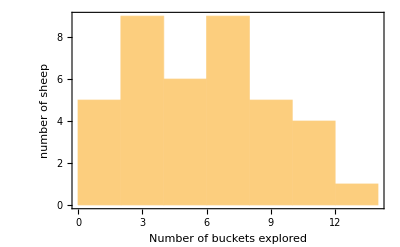

```mathematica
Histogram[Values[indexToMeanET],Frame->True,FrameLabel->{"Number of buckets explored","number of sheep"}]
```

### Herd composition

```mathematica
dbScanHerds50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/HerdSize/dbScanHerds50.mx"];
```

```mathematica
ETHerds=dbScanHerds50/.indexToMeanET/."NA"->Missing[];
```

```mathematica
averageET=Mean/@DeleteCases[DeleteCases[Catenate[ETHerds[[All,1;;-2]]],Missing[],2],{}];
```

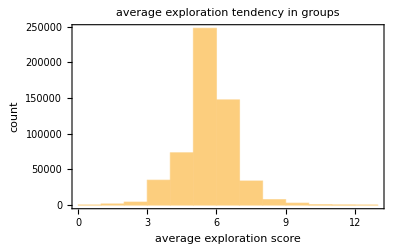

```mathematica
Histogram[averageET,{1},Frame->True,FrameLabel->{"average exploration score","count"},PlotLabel->"average exploration tendency in groups"]
```

### Time Spent alone

```mathematica
groupStability50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/groupStability50.mx"];
```

Import data on how long each sheep spent by itself.

```mathematica
groupToTimeAlone=Length/@KeySelect[SortBy[groupStability50,Length],Length[#]==1&][[;;51]];
```

```mathematica
indexToTimeAlone=Association[#->groupToTimeAlone[{#}]&/@Range[51]];
```

```mathematica
ETTimeAlone=DeleteCases[Table[{indexToMeanET[x],indexToTimeAlone[x]},{x,51}],{"NA",_}]
```

{{6.5,36868},{11.5,15594},{6.91667,3852},{9.,12785},{7.5,15385},{1.5,15503},{2.,11552},{3.25,20256},{4.25,9656},{4.66667,16911},{2.6,10357},{1.75,22185},{11.1667,8923},{0.333333,2667},{1.75,15945},{3.25,23039},{2.25,21234},{4.33333,9428},{1.25,13631},{8.5,18062},{3.75,8871},{12.5,10636},{9.,14145},{6.,8791},{2.75,14488},{7.91667,11568},{3.,11531},{8.4,15145},{5.33333,10979},{4.,14739},{4.5,15422},{6.25,13653},{10.25,6126},{7.25,14077},{8.5,10808},{2.66667,15161},{7.,6924},{10.75,12171},{6.,2963}}

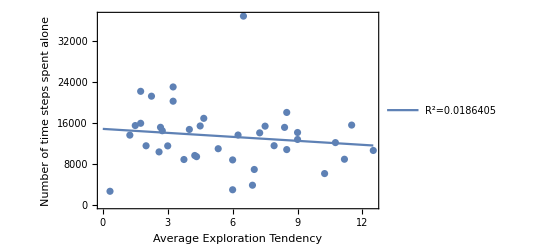

```mathematica
ResourceFunction["RegressionListPlot"][ETTimeAlone,Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Number of time steps spent alone",Medium]},"DisplayRSquared"->True]
```

### Average Group Size

```mathematica
indexToGroupLengths50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/indexToGroupLengths50.mx"];
```

```mathematica
indexToMeanGroupLength50 = MapAt[Mean,indexToGroupLengths50,All];
```

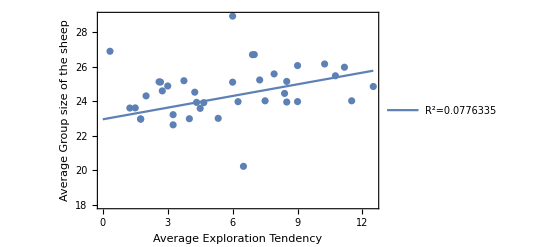

```mathematica
ResourceFunction["RegressionListPlot"][DeleteCases[Table[{indexToMeanET[x],indexToMeanGroupLength50[x]//N},{x,51}],{"NA",_}],Frame->True,FrameLabel->{Style["Average Exploration Tendency",Medium],Style["Average Group size of the sheep",Medium]},"DisplayRSquared"->True]
```